```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
Print["Package path ",FindFile["GDCComparisons`"]];
Print["Package path ",FindFile["GDCAnalysis5`"]];
<<GDCAnalysis3`
<<GDCComparisons`
<<GDCAnalysis5`
```

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis5.m

```mathematica
nEFUN[ind_, data_, eCON_]:=Module[{pers,persE,npersE, out},
pers=data[[All,ind]];
persE=Map[Union[#["BK"],#["EV"]]&,pers];
npersE=Map[Length[#]&,persE];
(*Print["npersE ", npersE];*)
out=Map[(eCON[[#]]+npersE[[#]])&,Range[Length[npersE]]];
Return[out];
];

eFUN[ind_, data_,dev_, mod_]:=Module[{pers,persE,persENEG, false,true, out},
pers=data[[All,ind]];
persE=Map[Union[#["BK"],#["EV"]]&,pers];
(*Print["persE ", persE];*)
(*Map[If[StringQ[#],!#,#[[1]]]&,ex]*)
persENEG=Map[Function[y,Map[Function[x,If[StringQ[x],!x,x[[1]]]],y]],persE];
(*Print["persENEG ", persENEG];*)
false=Map[Intersection[dev,#]&,persENEG];
true=Map[Intersection[dev,#]&,persE];
out=Which[mod=="FALN", Map[Length[#]&,false],
mod=="FAL",false,
mod=="TRUN", Map[Length[#]&,true],
mod=="TRU",true];
Return[out];
];

prozEFunc[eL_,sentPers_]:=Module[{out},
out=Map[Round[ eL[[#]]/sentPers[[#]],0.001]&,Range[Length[sentPers]]];
Return[out];
];
```

```mathematica
sigFiles=FileNames["/home/carla/GDC/CONF/DLB/GDC_Conf_AR_DLB_ALL_Out/*.out"];
tauFiles=FileNames["/home/carla/GDC/TAU2/*.out"];
posFiles=FileNames["/home/carla/GDC/POS/*.txt"];
pos=Map[Get[#]&,posFiles];
```

```mathematica
con=pos[[All,1]];
conE=Map[Union[#["BK"],#["EV"]]&,con];
```

```mathematica
sigs=Map[N[ToExpression[StringDrop[FindList[#,"sigma "][[1]],6]]]&,sigFiles]
sens=Map[ToExpression[StringDrop[FindList[#,"Number Sentences "][[3]],18]]&,tauFiles]
numCONE=Map[Length[#]&,conE]
(*sensPers=Map[sens[[#]]-numCONE[[#]]&,Range[Length[sens]]]*)
```

{79065.,2.22306×10^7,1.18149×10^8,2.03029×10^8,4.16805×10^9,6.28029×10^10,6.18737×10^11,4.2205×10^12,9.06856×10^12}

{46,65,84,88,102,110,117,123,132}

{8,9,15,17,21,22,22,23,26}

```mathematica
dens=Map[Round[((sens[[#]]-Log[sigs[[#]]])/sens[[#]]),0.01]&,Range[Length[sens]]]
```

{0.75,0.74,0.78,0.78,0.78,0.77,0.77,0.76,0.77}

```mathematica
SetDirectory["/home/carla/GDC/DENS/"]
```

/home/carla/GDC/DENS

```mathematica
Put[dens, "GDC_D_TAU_ROUNDED.txt"]
```

```mathematica
nameI=Map[{#,pos[[8,#]][["name"]]}&,Range[Length[pos[[8]]]]]
```

{{1,CON},{2,DEV},{3,DLB},{4,RP1},{5,SF1},{6,USS},{7,MUR},{8,CFP},{9,LYE},{10,LP1},{11,PHI},{12,LVF},{13,LVS},{14,AP1},{15,SED},{16,AP2},{17,LP2},{18,RP2},{19,AUS}}

```mathematica
eSIZE=<|nameI[[3,2]]->nEFUN[3,pos,numCONE],
nameI[[7,2]]->nEFUN[7,Drop[pos,1],Drop[numCONE,1]],
nameI[[9,2]]->nEFUN[9,Drop[pos,1],Drop[numCONE,1]],
nameI[[11,2]]->nEFUN[11,Drop[pos,2],Drop[numCONE,2]],
nameI[[15,2]]->nEFUN[15,Drop[pos,3],Drop[numCONE,3]],
nameI[[19,2]]->nEFUN[19,Drop[pos,6],Drop[numCONE,6]]|>
```

<|DLB→{15,22,22,25,33,36,39,42,43},MUR→{20,25,30,37,41,43,42,45},LYE→{19,22,26,31,35,36,41,43},PHI→{20,24,32,35,36,40,41},SED→{25,34,38,39,44,44},AUS→{40,44,43}|>

```mathematica
N[{2./20,5./20,8./20}]
```

{0.1,0.25,0.4}

```mathematica
vals=Values[eSIZE]
names={"DLB","MUR","LYE","PHI","SED","AUS"};
ePROZ=<|names[[1]]->prozEFunc[vals[[1]],sens],
names[[2]]->prozEFunc[vals[[2]],Drop[sens,1]],
names[[3]]->prozEFunc[vals[[3]],Drop[sens,1]],
names[[4]]->prozEFunc[vals[[4]],Drop[sens,2]],
names[[5]]->prozEFunc[vals[[5]],Drop[sens,3]],
names[[6]]->prozEFunc[vals[[6]],Drop[sens,6]]|>
```

{{15,22,22,25,33,36,39,42,43},{20,25,30,37,41,43,42,45},{19,22,26,31,35,36,41,43},{20,24,32,35,36,40,41},{25,34,38,39,44,44},{40,44,43}}

<|DLB→{0.326,0.338,0.262,0.284,0.324,0.327,0.333,0.341,0.326},MUR→{0.308,0.298,0.341,0.363,0.373,0.368,0.341,0.341},LYE→{0.292,0.262,0.295,0.304,0.318,0.308,0.333,0.326},PHI→{0.238,0.273,0.314,0.318,0.308,0.325,0.311},SED→{0.284,0.333,0.345,0.333,0.358,0.333},AUS→{0.342,0.358,0.326}|>

```mathematica
devABFIN=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Veritism/E_DEDAB/gdc_DEDAB_E_DEV.txt"][[-1]];
```

```mathematica
eFUN[3, pos,devABFIN]
```

{{!BCL CRT - CAM,!Characteristic Rock Type Principle,!MC CRT - CAM,!NC CRT - CAM,!Passing Devon Northwards},{!BCL CRT - CAM,!Characteristic Rock Type Principle,!MC CRT - CAM,!NC CRT - CAM,!Passing Devon Northwards},{!Passing Devon Northwards},{},{BCL - FA},{BCL - FA,Non-Culm - Body of Evidence - Fossils},{BCL - FA,!Devon Strata - Temporal Order - 3,!Non-Culm - Body of Evidence - Region},{BCL - FA,MC - FA,Non-Culm Fossil Mixture - Devon,!Non-Culm - Body of Evidence - Region,!Sequence of Strata - Tor Bay and Newton Abott},{}}

```mathematica
persInds={3,7,9,11,15,19};
persDrops={0,1,1,2,3,6};
```

```mathematica
eFALSE=Association[Map[names[[#]]->eFUN[persInds[[#]], Drop[pos,persDrops[[#]]],devABFIN,"FAL"]&,Range[6]]];
```

```mathematica
eFALSENUM=Association[Map[names[[#]]->eFUN[persInds[[#]], Drop[pos,persDrops[[#]]],devABFIN,"FALN"]&,Range[6]]]
eTRUENUM=Association[Map[names[[#]]->eFUN[persInds[[#]], Drop[pos,persDrops[[#]]],devABFIN,"TRUN"]&,Range[6]]]
```

<|DLB→{5,5,1,0,1,2,3,5,0},MUR→{2,2,2,4,4,7,1,0},LYE→{2,2,2,3,5,5,3,0},PHI→{0,0,0,1,2,3,0},SED→{0,3,4,5,6,0},AUS→{1,2,0}|>

<|DLB→{1,5,3,5,7,8,10,10,13},MUR→{6,3,5,4,7,6,12,12},LYE→{5,1,3,3,4,5,11,11},PHI→{2,4,7,8,8,10,11},SED→{4,5,7,7,10,13},AUS→{13,15,13}|>

```mathematica
sens-15.0
```

{31.,50.,69.,73.,87.,95.,102.,108.,117.}

```mathematica
8./19
4./19
```

0.421053

0.210526

```mathematica
valsFalse=Values[eFALSENUM]
valsTrue=Values[eTRUENUM]
```

{{5,5,1,0,1,2,3,5,0},{2,2,2,4,4,7,1,0},{2,2,2,3,5,5,3,0},{0,0,0,1,2,3,0},{0,3,4,5,6,0},{1,2,0}}

{{1,5,3,5,7,8,10,10,13},{6,3,5,4,7,6,12,12},{5,1,3,3,4,5,11,11},{2,4,7,8,8,10,11},{4,5,7,7,10,13},{13,15,13}}

```mathematica
eFALSEPROZ=Association[Map[names[[#]]->prozEFunc[valsFalse[[#]],Drop[sens-15.,persDrops[[#]]]]&,Range[6]]]
eTRUEPROZ=Association[Map[names[[#]]->prozEFunc[valsTrue[[#]],Drop[sens-15,persDrops[[#]]]]&,Range[6]]]
```

<|DLB→{0.161,0.1,0.014,0.,0.011,0.021,0.029,0.046,0.},MUR→{0.04,0.029,0.027,0.046,0.042,0.069,0.009,0.},LYE→{0.04,0.029,0.027,0.034,0.053,0.049,0.028,0.},PHI→{0.,0.,0.,0.011,0.02,0.028,0.},SED→{0.,0.034,0.042,0.049,0.056,0.},AUS→{0.01,0.019,0.}|>

<|DLB→{0.032,0.1,0.043,0.068,0.08,0.084,0.098,0.093,0.111},MUR→{0.12,0.043,0.068,0.046,0.074,0.059,0.111,0.103},LYE→{0.1,0.014,0.041,0.034,0.042,0.049,0.102,0.094},PHI→{0.029,0.055,0.08,0.084,0.078,0.093,0.094},SED→{0.055,0.057,0.074,0.069,0.093,0.111},AUS→{0.127,0.139,0.111}|>

```mathematica
h[nam_]:=Module[{list},
list=Which[nam=="DLB",Range[9],
nam=="MUR",Drop[Range[9],1],
nam=="LYE",Drop[Range[9],1],
nam=="PHI",Drop[Range[9],2],
nam=="SED",Drop[Range[9],3],
nam=="AUS",Drop[Range[9],6]
];
Return[list];];
pointsE1=Association[Map[Function[y,
y->Map[Function[x,{eFALSEPROZ[y][[x]],eTRUEPROZ[y][[x]],h[y][[x]]}],Range[Length[ePROZ[y]]]]],names]]
```

<|DLB→{{0.161,0.032,1},{0.1,0.1,2},{0.014,0.043,3},{0.,0.068,4},{0.011,0.08,5},{0.021,0.084,6},{0.029,0.098,7},{0.046,0.093,8},{0.,0.111,9}},MUR→{{0.04,0.12,2},{0.029,0.043,3},{0.027,0.068,4},{0.046,0.046,5},{0.042,0.074,6},{0.069,0.059,7},{0.009,0.111,8},{0.,0.103,9}},LYE→{{0.04,0.1,2},{0.029,0.014,3},{0.027,0.041,4},{0.034,0.034,5},{0.053,0.042,6},{0.049,0.049,7},{0.028,0.102,8},{0.,0.094,9}},PHI→{{0.,0.029,3},{0.,0.055,4},{0.,0.08,5},{0.011,0.084,6},{0.02,0.078,7},{0.028,0.093,8},{0.,0.094,9}},SED→{{0.,0.055,4},{0.034,0.057,5},{0.042,0.074,6},{0.049,0.069,7},{0.056,0.093,8},{0.,0.111,9}},AUS→{{0.01,0.127,7},{0.019,0.139,8},{0.,0.111,9}}|>

```mathematica
{{Min[Flatten[Values[pointsE1],1][[All,1]]],Max[Flatten[Values[pointsE1],1][[All,1]]]},
{Min[Flatten[Values[pointsE1],1][[All,2]]],Max[Flatten[Values[pointsE1],1][[All,2]]]}}
```

{{0.,0.161},{0.014,0.139}}

```mathematica
singlePlot2[nam_, dataArrows_,poi_,colS_,type_]:=Module[{head,arrows,size, plot1,pointsG,plot2,dataInset,boxInset},

head=Graphics[{Thickness[0.007],Line[{{{-1,1/2},{0,0},{-1,-1/2}}}]}];
arrows=bowedArrowsData[dataArrows];

dataInset={{"Circles", ToString[type]},{"PERS",ToString[nam]}};
boxInset=Text@Grid[dataInset,Background->{None,{Lighter[Yellow,.9],{White,Lighter[Black,.9]}}},
Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},
Alignment->{{Left,Center}},ItemSize->{{6,4}},Frame->Darker[Gray,.6],ItemStyle->17,Spacings->{Automatic,.8}];


plot1=Graphics[{Opacity[0.4],colS[[#4]],Arrowheads[{{.012,1,{head,0.01}}}],Thickness[0.007],Arrow[BezierCurve[{#1,#2,#3}]]}&@@@arrows,PlotRange->{{0.,0.161},{0.014,0.139}},
Frame->True,FrameLabel->{Style["EFALSEPROZ",20],Style["ETRUEPROZ",20]}, 
ImageSize->800, ImagePadding->120,Epilog->Inset[Style[boxInset,16],{0.135,0.125}]];

Print["poi ", poi];
size=Map[(Log[poi[[#,3]]]*0.07)+0.07&,Range[Length[poi]]];
Print["size ", size];
pointsG=Map[Graphics[{Opacity[0.6],Hue[1,0.3],PointSize[size[[#]]],Point[poi[[#]][[1;;2]]]}]&, Range[Length[poi]]];
plot2=Show[Catenate[{{plot1},pointsG}]];

Return[plot2];
];

pointsFunc[nL_, pDL_,threC_, pE_]:=Module[{out},
out=Map[Function[y,nL[[y]]->Map[Function[x,Flatten[{pE[nL[[y]]][[threC[nL[[y]]][[x,1]]-pDL[[y]]]][[1;;2]],threC[nL[[y]]][[x,2]]},1]],Range[Length[threC[nL[[y]]]]]]],Range[Length[nL]]];
Return[out];]
```

```mathematica
timesteps=Range[9];
col2=Map[Blend[{Blue, Yellow},#]&,Range[Length[timesteps]]/Length[timesteps]]
```

{RGBColor[Rational[1, 9], Rational[1, 9], Rational[8, 9]],RGBColor[Rational[2, 9], Rational[2, 9], Rational[7, 9]],RGBColor[Rational[1, 3], Rational[1, 3], Rational[2, 3]],RGBColor[Rational[4, 9], Rational[4, 9], Rational[5, 9]],RGBColor[Rational[5, 9], Rational[5, 9], Rational[4, 9]],RGBColor[Rational[2, 3], Rational[2, 3], Rational[1, 3]],RGBColor[Rational[7, 9], Rational[7, 9], Rational[2, 9]],RGBColor[Rational[8, 9], Rational[8, 9], Rational[1, 9]],RGBColor[1, 1, 0]}

```mathematica
confVal=Get["/home/carla/GDC/CH_Pool/VV_Tables/THRE_RATIO_TIME.txt"];
```

```mathematica
dojCirc=Values[confVal][[All,1]][[All,2]][[All,2]];
zCirc=Values[confVal][[All,2]][[All,2]][[All,2]];
fCirc=Values[confVal][[All,3]][[All,2]][[All,2]];
```

```mathematica
timeRules={"S8b"->9, "S7b"->8,"S6b"->7,"S5b"->6,"S4b"->5,"S3b"->4,"S2b"->3,"S1b"->2,"S0b"->1};threDOJ=Association[Map[names[[#]]->Cases[dojCirc[[#]],p_/;StringMatchQ[p[[1]],"S*b"]]&,Range[6]]]/.timeRules
threZ=Association[Map[names[[#]]->Cases[zCirc[[#]],p_/;StringMatchQ[p[[1]],"S*b"]]&,Range[6]]]/.timeRules
threF=Association[Map[names[[#]]->Cases[fCirc[[#]],p_/;StringMatchQ[p[[1]],"S*b"]]&,Range[6]]]/.timeRules
```

<|DLB→{{9,1}},MUR→{{6,34/67},{8,1},{9,1}},LYE→{{7,2/3},{8,1},{9,1}},PHI→{{5,7/10},{6,7/10},{7,7/10},{8,1},{9,1}},SED→{{9,1}},AUS→{{7,11/15},{8,1},{9,1}}|>

<|DLB→{{9,1}},MUR→{{6,8/9},{8,1},{9,1}},LYE→{{7,1},{8,1},{9,1}},PHI→{{5,1},{6,1},{7,1},{8,1},{9,1}},SED→{{9,1}},AUS→{{7,1},{8,1},{9,1}}|>

<|DLB→{{9,1}},MUR→{{6,8/9},{8,1},{9,1}},LYE→{{7,1},{8,1},{9,1}},PHI→{{5,1},{6,1},{7,1},{8,1},{9,1}},SED→{{9,1}},AUS→{{7,1},{8,1},{9,1}}|>

```mathematica
pDOJass=Association[pointsFunc[names, persDrops,threDOJ, pointsE1]]
pZass=Association[pointsFunc[names, persDrops,threZ, pointsE1]];
pFass=Association[pointsFunc[names, persDrops,threF, pointsE1]]
```

<|DLB→{{0.,0.111,1}},MUR→{{0.042,0.074,34/67},{0.009,0.111,1},{0.,0.103,1}},LYE→{{0.049,0.049,2/3},{0.028,0.102,1},{0.,0.094,1}},PHI→{{0.,0.08,7/10},{0.011,0.084,7/10},{0.02,0.078,7/10},{0.028,0.093,1},{0.,0.094,1}},SED→{{0.,0.111,1}},AUS→{{0.01,0.127,11/15},{0.019,0.139,1},{0.,0.111,1}}|>

<|DLB→{{0.,0.111,1}},MUR→{{0.042,0.074,8/9},{0.009,0.111,1},{0.,0.103,1}},LYE→{{0.049,0.049,1},{0.028,0.102,1},{0.,0.094,1}},PHI→{{0.,0.08,1},{0.011,0.084,1},{0.02,0.078,1},{0.028,0.093,1},{0.,0.094,1}},SED→{{0.,0.111,1}},AUS→{{0.01,0.127,1},{0.019,0.139,1},{0.,0.111,1}}|>

poi {{0.,0.111,1}}

size {0.07}

poi {{0.042,0.074,34/67},{0.009,0.111,1},{0.,0.103,1}}

size {0.0225168,0.07,0.07}

poi {{0.049,0.049,2/3},{0.028,0.102,1},{0.,0.094,1}}

size {0.0416174,0.07,0.07}

poi {{0.,0.08,7/10},{0.011,0.084,7/10},{0.02,0.078,7/10},{0.028,0.093,1},{0.,0.094,1}}

size {0.0450328,0.0450328,0.0450328,0.07,0.07}

poi {{0.,0.111,1}}

size {0.07}

poi {{0.01,0.127,11/15},{0.019,0.139,1},{0.,0.111,1}}

size {0.0482892,0.07,0.07}

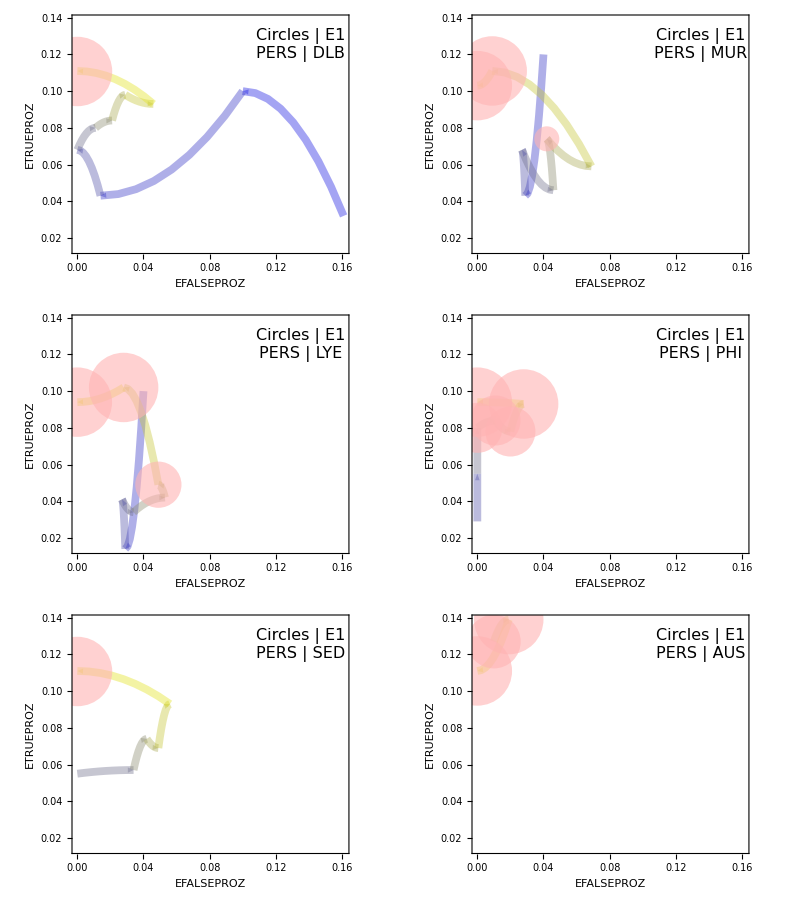

```mathematica
dojTHRE=Map[singlePlot2[#, pointsE1[#],pDOJass[#],col2,"E1"]&,names];
dojGrid=Grid[{dojTHRE[[1;;2]],dojTHRE[[3;;4]],dojTHRE[[5;;6]]}]
```